## Sierpinski

```mathematica
sierpinskize[g_]:=Module[{g0,g1,g2},
g0=g;
g1=Translate[g0,{1,0}];
g2=Translate[g0,{1/2,√3/2}];
Scale[{g0,g1,g2},1/2,{0,0}]
];
```

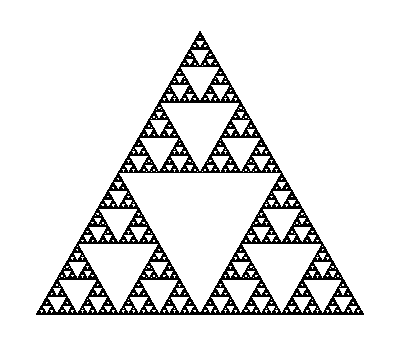

/home/nicolas/git/talks/2020 fractals/sierpinksi_triangle_7.pdf

```mathematica
i=7;
Graphics[Nest[sierpinskize,Triangle[{{0,0},{1,0},{1/2,(√3)/2}}],i]]
Export[NotebookDirectory[]<>"sierpinksi_triangle_"<>ToString[i]<>".pdf",%]
```

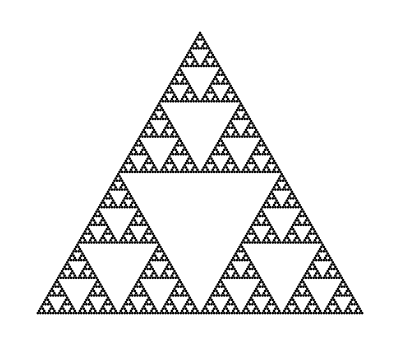

```mathematica
Graphics[Nest[sierpinskize,Disk[{0,0},0.5],7]]
```

```mathematica
Export[NotebookDirectory[]<>"sierpinksi_ball_Infty.pdf",%]
```

/home/nicolas/sierpinksi_ball_Infty.pdf

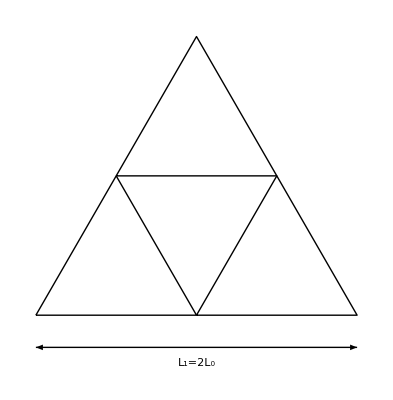

```mathematica
(* base triangle *)
t0=Line[{{0,0},{1,0},{1/2,√3/2},{0,0}}];
Graphics[{Nest[sierpinskize,t0,1],{Arrowheads[{-.04,.04}],Arrow@Line[{{0,-.1},{1,-.1}}]},Text[Style["L_1=2L_0",Large,Italic],{0.5,-.15}]}]
```

```mathematica
Export[NotebookDirectory[]<>"scale1.pdf",%]
```

/home/nicolas/scale1.pdf

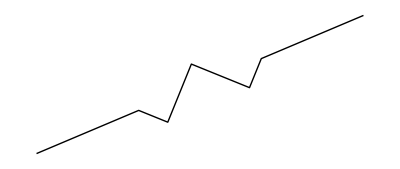

```mathematica
n=3;
(* represent a line of length 1, of origin O, making an angle θ with the horizontal axis, with n oscillations *)
(* the oscillations occupy a fraction 1-2t of the line *)
res[t_,O_,θ_]:=Scale[Rotate[Translate[Line[{{0,0},{1+t,0}}~Join~Table[{2i+t,(-1)^i},{i,1,n}]~Join~{{2n+1+t,0},{2(n+1+t),0}}],O],θ,O],1/(2(n+1+t)),O];
Graphics[res[4,{0,0},0.4]]
```

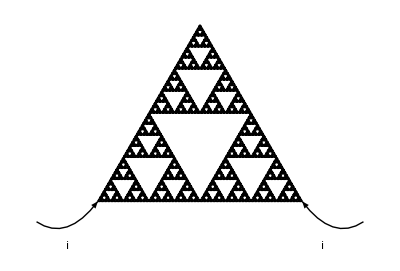

```mathematica
t=4;
n=6;
t1={res[t,{0,0},0],res[t,{0,0},Pi/3],res[t,{1,0},2Pi/3]};
Graphics[t1];
Graphics[{Nest[sierpinskize,t1,6],Text[Style["i",Large,Italic],{-.15,-.22}],Text[Style["i",Large,Italic],{1.1,-.22}],{Arrowheads[{{.04,.6}}],Arrow@BezierCurve[{{-.3,-.1},{-.15,-.2},{0,0}}]},{Arrowheads[{{-.04,.4}}],Arrow@BezierCurve[{{1.3,-.1},{1.15,-.2},{1,0}}]}}]
```

```mathematica
Export[NotebookDirectory[]<>"resInfty.pdf",%]
```

/home/nicolas/resInfty.pdf

```mathematica
leafize[g_]:=Module[{g0,g1,g2,θ1=Pi/2-0.2,θ2=-Pi/2+0.2,s1=1.,s2=1.2},
g0=Rotate[g,-Pi/12];
g1=Scale[Rotate[Translate[g0,{-0.1,-0.2}],θ1],s1];
g2=Scale[Rotate[Translate[g0,{0.1,-0.2}],θ2],s2];
Scale[{g0,g1,g2},1/2,{0,0}]
];
```

```mathematica
Graphics[Nest[leafize,Rectangle[{0,0},{.1,.1}],3]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"leafInfty.pdf",%]
```

/home/nicolas/leafInfty.pdf

```mathematica
leafize2[g_]:=Module[{g0,g1,g2,g3,g4,θ1=Pi/2,s1=√1},
g0=Rotate[g,0];
g1=Translate[Rotate[Scale[g,s1],θ1],{(√2+s1)/2,-(√2+s1)/2}/√2];
g2=Translate[g,2{(√2+s1)/2,-(√2+s1)/2}/√2];
g3=Translate[g,2{0,-(√2+s1)/2}/√2];
g4=Translate[g,2{(√2+s1)/2,0}/√2];
Scale[{g0,g1,g2,g3,g4},1/2,{0,0}]
];
```

```mathematica
Graphics[Nest[leafize2,Rectangle[{0,0},{1,1}],5]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"dragon.png",%,ImageSize->1200]
```

/home/nicolas/dragon.png

## Julia

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
new=RGBColor["#7f0033"];
```

```mathematica
new
```

RGBColor[0.4980392156862745, 0., 0.2]

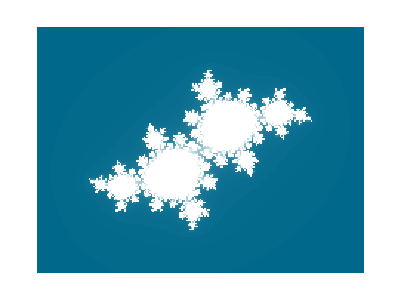

```mathematica
c=-.39-.59I;
JuliaSetPlot[c,ColorFunction -> (If[#3==1,White,Lighter[BostonBlue,#3]]&),Frame->False,ImageResolution->220,PlotRange->{{-2,2},{-1.5,1.5}}]
```

```mathematica
Export[NotebookDirectory[]<>"juliaScreen.png",%,ImageSize->2200]
```

/home/nicolas/juliaScreen.png

```mathematica
c=-.39-.59I;
JuliaSetPlot[c,ColorFunction -> (If[#3==1,White,Lighter[BostonBlue,#3]]&),Frame->False,ImageResolution->1200]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"juliaBis.png",%,ImageSize->1200]
```

/home/nicolas/juliaBis.png

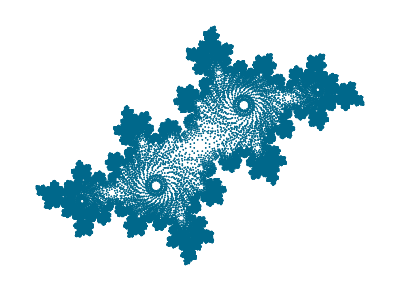

```mathematica
p=JuliaSetPlot[c,ColorFunction->None,PlotStyle->Opacity[1.,BostonBlue],Frame->False]
```

```mathematica
Export[NotebookDirectory[]<>"julia2.png",p,ImageSize->1200]
```

/home/nicolas/julia2.png

## Fibonacci

```mathematica
h[n_,ρ_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
n=14;
{sp,vp}=Eigensystem[h[n,.6]];
o=Ordering[sp];
vp=vp[[o]];
sp=sp[[o]];
```

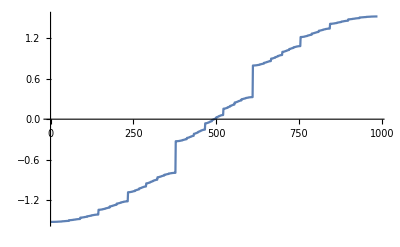

```mathematica
ListPlot[sp,Joined->True]
```

```mathematica
(* shift spectrum to fit into the unit interval *)
sp=(sp-sp[[1]])/(sp[[-1]]-sp[[1]]);
idos=Table[{sp[[i]],i/Fibonacci[n+2]},{i,Fibonacci[n+2]}];
```

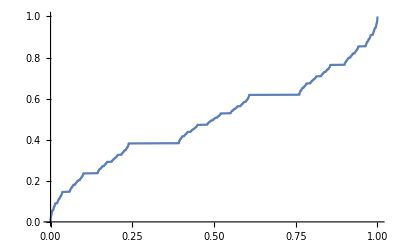

```mathematica
ListPlot[idos,Joined->True]
```

```mathematica
FirstPosition[idos,it_/;it>0.4]
```

{395,2}

```mathematica
idos[[%]]//N
```

{{0.396043,0.400203},{1.21971×10^-6,0.00202634}}

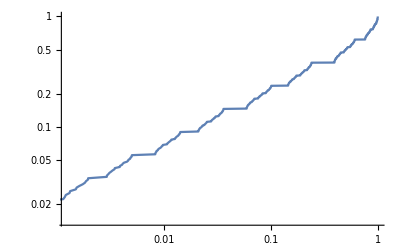

```mathematica
ListLogLogPlot[idos,Joined->True]
```